```mathematica
ClearAll[a,b,c,α,β,p]
```

```mathematica
p=0.13 (* range от 0 до 1 *)
```

0.13

```mathematica
modelZ= Abs[(1-(((1+α)*Exp[-b*t]))/(1+α*Exp[-b*t]))^{(c/b)*(p-β)}] * (a/(p-β))
```

{(a Abs[(1-(ⅇ^(-b t) (1+α))/(1+ⅇ^(-b t) α))^((c (0.13-β))/b)])/(0.13-β)}

```mathematica
dataZhang = {{1,16},{2,24},{3,27},{4,33},{5,41},{6,46},{7,54},{8,58},{9,69},{10,75},{11,81},{12,86},{13,90},{14,93},{15,96},{16,98},{17,99},{18,100},{19,100},{20,100}}
```

{{1,16},{2,24},{3,27},{4,33},{5,41},{6,46},{7,54},{8,58},{9,69},{10,75},{11,81},{12,86},{13,90},{14,93},{15,96},{16,98},{17,99},{18,100},{19,100},{20,100}}

```mathematica
fitt = FindFit[dataZhang, modelZ, {a,b,β,α,c},t] ;
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
eval = Evaluate[modelZ/.fitt];
```

```mathematica
modelFunc = Function[{t}, Evaluate[eval]];
```

```mathematica
epilog = Epilog->Map[Point,dataZhang];
```

```mathematica
plotRange = PlotRange->{0,150};
```

```mathematica
axesOrigin = AxesOrigin->{0,0};
```

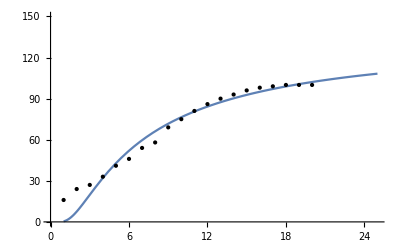

```mathematica
Plot[modelFunc[t], {t, 1,25},Evaluate[epilog] ,Evaluate[plotRange] , Evaluate[axesOrigin]]
```